# Introduction à la science des données

## Machine Learning

Nous allons considérer un problème courant sur le marché immobilier en région parisienne. 
Comment prédire le prix d’un logement en région parisienne à partir des données en notre possession ?
Pour commencer, nous simplifions le problème et on considère uniquement la surface d’habitation comme unique donnée en notre possession.
Ainsi, on souhaite prédire le prix d’un logement de 50m.b2 en région parisienne.

Pour effectuer, cette prédiction nous avons une base de données contenant 10 prix de logements avec la surface habitable.
Surfaces  (en m.b2) | 35
Prix (en euros) | 15000038
18050045
24000055
27000059
28550060
30550063
31500064
32000070
37000071
375500

```mathematica
m = 10 ;
Surface = {35,38,45,55,59,60,63,64,70,71} ;
Prix = {150000,180500,240000,270000,285500,305500,315000,320000,370000,375500};
data = Flatten[{Surface,Prix},{2}]
```

{{35,150000},{38,180500},{45,240000},{55,270000},{59,285500},{60,305500},{63,315000},{64,320000},{70,370000},{71,375500}}

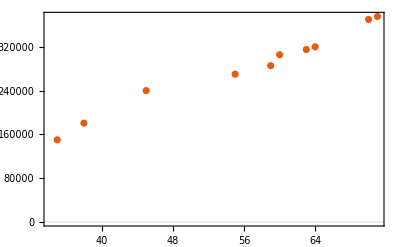

```mathematica
ListPlot[data,PlotTheme->"Scientific"]
```

Afin de prédire le prix du logement de 50m.b2, on peut déterminer l’équation de la droite qui passe “au plus proche” des 10 points

```mathematica
Manipulate[With[{vala=a, valb=b},Show[{ListPlot[data,PlotTheme->"Scientific",PlotStyle->Red], Plot[vala*x+valb,{x,0,100},PlotLegends->"AllExpressions"]}]],{a,0,15000},{b,-300000,300000}]
```

On peut observer qu’il n’est pas facile d’obtenir l’équation la plus parfaite possible mais s’il semble que pour une équation proche de  y=6400x-70000 nous soyons proche de ce qu’il faut.
Pour vérifier, si on ne peut pas améliorer notre approche, il faudrait déterminer les valeurs de a et b dans l’équation de la droite y=a x+b qui permettent de minimiser la distance entre les points et la droite.

```mathematica
Manipulate[With[{vala=a, valb=b},Show[{ListPlot[data,PlotTheme->"Scientific",PlotStyle->Red], Plot[vala*x+valb,{x,0,100},PlotLegends->"AllExpressions"],Graphics[Line[{#,{#⟦1⟧,vala*#⟦1⟧+valb}}]&/@data]}]],{a,0,15000},{b,-300000,300000}]
```

Il existe plusieurs façon de calculer cette distance entre les points et la droite : 
- Soit par la MAE (Mean Absolute Error) : 1/m∑_(i=1)^m|y_i-(a x_i+b)|
- Soit par la RMSE (Root Mean Square Error) : √(1/m∑_(i=1)^m (y_i-(a x_i+b))^2)

```mathematica
MAE[a_,b_]:=(1/m)*Total[Abs[#⟦2⟧-(a*#⟦1⟧+b)]&/@data]
RMSE[a_,b_]:=√(1/m*Total[(#⟦2⟧-(a*#⟦1⟧+b))^2&/@data])
Row[{Plot3D[MAE[a,b],{a,0,15000},{b,-300000,300000},ImageSize->400],Plot3D[RMSE[a,b],{a,0,15000},{b,-300000,300000},ImageSize->400]}]
```

-Graphics3D--Graphics3D-

```mathematica
Manipulate[With[{vala=a, valb=b},Column[{Show[{ListPlot[data,PlotTheme->"Scientific",PlotStyle->Red,ImageSize->500], Plot[vala*x+valb,{x,0,100},PlotLegends->"AllExpressions"],Graphics[Line[{#,{#⟦1⟧,vala*#⟦1⟧+valb}}]&/@data]}],
Row[{Show[Plot3D[MAE[a,b],{a,0,15000},{b,-300000,300000},ImageSize->400,Mesh->None],Graphics3D[{PointSize[0.03],Point[{vala,valb,MAE[vala,valb]}]}]],Show[Plot3D[RMSE[a,b],{a,0,15000},{b,-300000,300000},ImageSize->400,Mesh->None],Graphics3D[{PointSize[0.03],Point[{vala,valb,RMSE[vala,valb]}]}]]}]}]],{a,0,15000},{b,-300000,300000}]
```

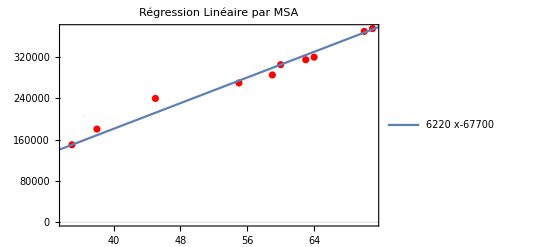
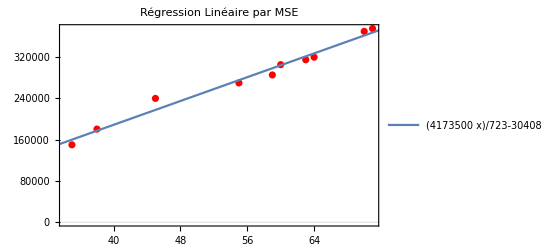

Le coût par MAE est de 8124

Le coût par RMSE est de 10142.7

```mathematica
sol1 = Minimize[MAE[a,b],{a,b}];
{a1,b1}={a,b}/.sol1⟦2⟧;

sol2 = Minimize[RMSE[a,b],{a,b}];
{a2,b2}={a,b}/.sol2⟦2⟧;

Row[{With[{vala=a1, valb=b1},Show[{ListPlot[data,PlotTheme->"Scientific",PlotStyle->Red,PlotLabel->"Régression Linéaire par MSA",ImageSize->400], Plot[vala*x+valb,{x,0,100},PlotLegends->"AllExpressions"]}]],
With[{vala=a2, valb=b2},Show[{ListPlot[data,PlotTheme->"Scientific",PlotStyle->Red,PlotLabel->"Régression Linéaire par MSE",ImageSize->400], Plot[vala*x+valb,{x,0,100},PlotLegends->"AllExpressions"]}]]}]
Print["Le coût par MAE est de ", sol1[[1]]]
Print["Le coût par RMSE est de ",N[sol2[[1]]]]
```

```mathematica
Print["La prédiction par MSA du prix d'un logement à 50m.b2 est de ", a1*50+b1," euros"]
Print["La prédiction par MSE du prix d'un logement à 50m.b2 est de ", N[a2*50+b2]," euros"]
```

La prédiction par MSA du prix d'un logement à 50m.b2 est de 243300 euros

La prédiction par MSE du prix d'un logement à 50m.b2 est de 246565. euros

## Comment utiliser Mathematica pour faire du Machine Learning

```mathematica
trainset =Flatten[ {#[[1]]->#[[2]]}&/@data]
p= Predict[trainset]
p[55]
```

{35→150000,38→180500,45→240000,55→270000,59→285500,60→305500,63→315000,64→320000,70→370000,71→375500}

PredictorFunction[…]

275306.

```mathematica
figure={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
area = {40.2,8.9,11.,4.9,13.6,15.6,14.7,3.8,34.7,10.8,4.,16.1,3.3,8.3,12.6};
data2 = Flatten[{figure,area},{2}];
trainset =Flatten[ {#[[1]]->#[[2]]}&/@data2]
p= Predict[trainset]
p[{-Graphics-,-Graphics-,-Graphics-}]
```

{-Graphics-→40.2,-Graphics-→8.9,-Graphics-→11.,-Graphics-→4.9,-Graphics-→13.6,-Graphics-→15.6,-Graphics-→14.7,-Graphics-→3.8,-Graphics-→34.7,-Graphics-→10.8,-Graphics-→4.,-Graphics-→16.1,-Graphics-→3.3,-Graphics-→8.3,-Graphics-→12.6}

PredictorFunction[…]

{30.1667,9.33333,9.33333}